```mathematica
eq =(x+ Exp[ϵ x])(x-Exp[ϵ x])
```

(-ⅇ^(x ϵ)+x) (ⅇ^(x ϵ)+x)

```mathematica
Solve[eq==0, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-ProductLog[-√(ϵ^2)]/ϵ},{x→-ProductLog[√(ϵ^2)]/ϵ}}

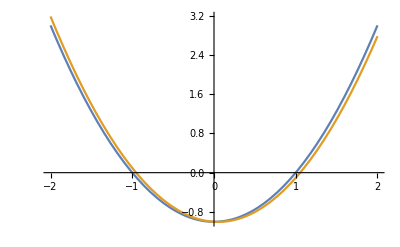

```mathematica
Plot[{eq/.ϵ->0, eq/.ϵ-> 0.05}, {x,-2,2}]
```

Here, we define the equation for the value of x:

```mathematica
approxEq= eq/.x-> y0 + ϵ y1 + ϵ^2 y^2
```

(-ⅇ^(ϵ (y0+y1 ϵ+y^2 ϵ^2))+y0+y1 ϵ+y^2 ϵ^2) (ⅇ^(ϵ (y0+y1 ϵ+y^2 ϵ^2))+y0+y1 ϵ+y^2 ϵ^2)

```mathematica
sol0 -> Solve[0 == approxEq /. ϵ -> 0, y0]
```

sol0→{{y0→-1},{y0→1}}

Try a series expansion

```mathematica
Series[approxEq, {ϵ, 0, 1}]
```

(-1+y0) (1+y0)+2 (-y0+y0 y1) ϵ+O[ϵ]^2